# 感知器算法

平面上有颜色不同的两类点，我们希望找到一条直线，将这两类点尽可能地隔开，这就是机器学习中的最简单的分类问题。

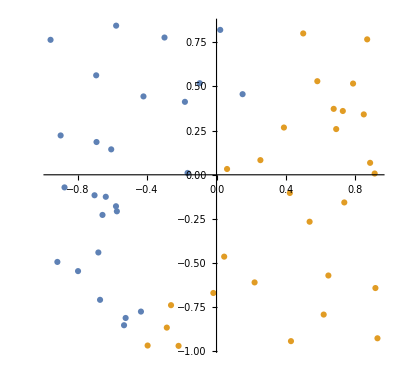

```mathematica
A=Select[RandomReal[{-1,1},{50,2}],2#[[1]]<#[[2]]&];
B=Select[RandomReal[{-1,1},{50,2}],2#[[1]]>#[[2]]&];
ListPlot[{A,B},AspectRatio->Automatic]
```

我们先以原点为起点，任取待分类的一点为中点，得到一个向量 w_0 ，再以 w_0 为法向量作一条过原点的直线。

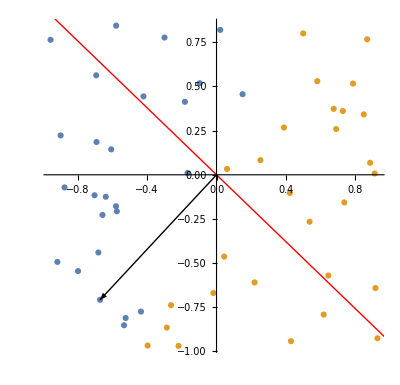

```mathematica
W0=A[[1]];
Show[ListPlot[{A,B},AspectRatio->Automatic],Graphics[{{Red,InfiniteLine[{0,0},Reverse[W0]*{1,-1}]},Arrow[{{0,0},W0}]}]]
```

显然，这样的一条直线是很粗糙的，我们应该想办法去修正它。为了便于描述，我们把蓝色的点标记为1，而黄色的点标记为-1，这些点记为 x_i，他们对应的标记为 y_i。那么，如果 sgn(w_0.x_i)=y_i，就说明这个点已经被正确分类。如果 x_i还没有被正确分类，我们就专门为 x_i去调整直线的法向量： w_1=w_0+y_i x_i 。

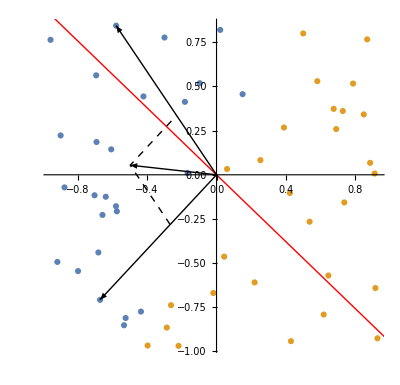

```mathematica
W1=W0;
Do[If[MemberQ[A,X],y=1,y=-1];If[Sign[W1.X]!=y,error=X;W1+=y X;Break[]],{X,A~Union~B}];
Show[ListPlot[{A,B},AspectRatio->Automatic],Graphics[{{Red,InfiniteLine[{0,0},Reverse[W0]*{1,-1}]},Arrow[{{{0,0},W0},{{0,0},error},{{0,0},Normalize[W1]/2}}],{Dashed,Line[{W0,W1,error}/(2Norm[W1])]}}]]
```

这样，再以 w_1为新的法向量，作一条过原点的直线，就能把之前分类错误的点正确分类了。

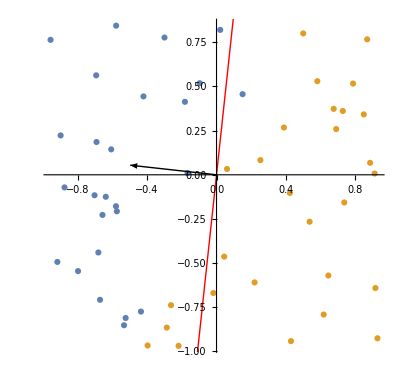

```mathematica
Show[ListPlot[{A,B},AspectRatio->Automatic],Graphics[{{Red,InfiniteLine[{0,0},Reverse[W1]*{1,-1}]},Arrow[{{0,0},1/2Normalize[W1]}]}]]
```

不过目前还是没有将全部的点分类正确，所以我们可以继续重复前面的调整步骤。可以证明，当真的存在一条“完美”的分隔直线时，这样的算法是收敛的。证明过程见http://nyuls.com/2018/10/02/perceptron-learning-algorithm/

下面是完整的迭代过程。

```mathematica
n=8;
W=A[[1]];
WList=Table[Do[If[MemberQ[A,X],y=1,y=-1];If[Sign[W.X]!=y,W+=y X;Break[]],{X,A~Union~B}];W,{n}]~Prepend~A[[1]];
ListAnimate[Table[Show[ListPlot[{A,B},AspectRatio->Automatic],Graphics[{{Red,InfiniteLine[{0,0},Reverse[WList[[i]]]*{1,-1}]},Arrow[{{0,0},Normalize[WList[[i]]]/2}]}]],{i,1,n+1}],AnimationRepetitions->1]
```

下面的数据不是线性可分的，感知器算法对此不再适用。

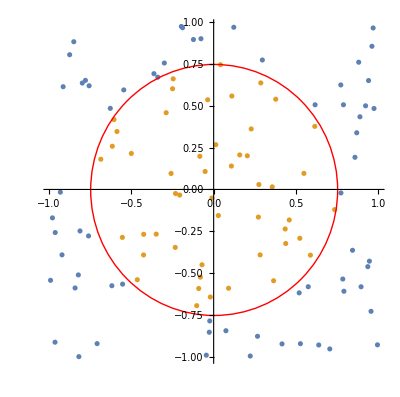

```mathematica
Show[ListPlot[{Select[RandomReal[{-1,1},{100,2}],Norm[#]>3/4&],Select[RandomReal[{-1,1},{100,2}],Norm[#]<3/4&]},AspectRatio->Automatic],Graphics[{Red,Circle[{0,0},3/4]}]]
```